#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy]
Off[LinearSolve::luc]
readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];
```

```mathematica
ClearAll;
ImgSize=900;
hbarc=197.32858;
hat[l_]:=Sqrt[2 l+1];
resultsDir="/home/kirscher/kette_repo/ComptonLIT/systems/mul_deuteron_miwchan/results";
tmpDir="/home/kirscher/kette_repo/ComptonLIT/systems/tmp";
SetDirectory[resultsDir]
```

/home/kirscher/kette_repo/ComptonLIT/systems/mul_deuteron_miwchan/results

Experimental results for the total cross section for deuteron photodisintegration
(W. Jaus & W.S. Woolcock -- Nuclear Physics A473 (1987) 685-704)
[σ_tot]=μb=10^-4 fm^2
[Lab photon energy] = MeV

```mathematica
DeutDataMuBarn=ReadList["../../../data/deuteron_diss_tot_exp.dat",Number,RecordLists->True];
DeutDataFm2=Transpose[{Transpose[DeutDataMuBarn][[1]],Transpose[DeutDataMuBarn][[2]] 10.^(-4)}];
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={0,1,2};
J0=1;
mIns=Range[-#,#,1]&/@Subscript[I, n];

thresholdLIT=10.8^(-8);
thresholdD=thresholdLIT;
```

```mathematica
Clear[matSqrts];matSqrts[norm_,cutoff_:0]:=Block[{es=Eigensystem[norm],ovsqi,ovsq,n},Print["min/max: ",MinMax[es[[1]]]];n=Length[Select[es[[1]],#<cutoff&]];Print["(min/max) discarded elements: ",n," ",MinMax[Select[es[[1]],#<cutoff&]]];

ovsq=DiagonalMatrix[If[#<cutoff,0,Sqrt[#]]&/@es[[1]]];ovsqi=DiagonalMatrix[If[#<cutoff,0,1/Sqrt[#]]&/@es[[1]]];
{Drop[ovsq.es[[2]],-n],Transpose[Drop[ovsqi.es[[2]],-n]]}]
```

### Read LHS ⟨ ϕ_D^n|(Ĥ)_(V18+UIX)|ϕ_D^m ⟩, m,n∈{1,N_D}

```mathematica
DNormHamMat=readREAL8list["./mat_np1^+"];
DBasisDim=IntegerPart[Sqrt[Length[DNormHamMat] 0.5]];
DNorm=ArrayReshape[DNormHamMat[[1;;DBasisDim^2]],{DBasisDim,DBasisDim}];
DHam=ArrayReshape[DNormHamMat[[DBasisDim^2+1;;]],{DBasisDim,DBasisDim}];
```

```mathematica
{DNmh,DNmhi}=matSqrts[DNorm,0.2];
```

min/max: {2.26381×10^-8,9.66562}

(min/max) discarded elements: 27 {2.26381×10^-8,0.185348}

#### The real calculation

Set a sensible cut-off

min/max: {2.26381×10^-8,9.66562}

(min/max) discarded elements: 0 {∞,-∞}

B(D) = -2.22233

Dim_full^deuteron = 40=^!40   ;     Dim_(non - singular)^deuteron = 40

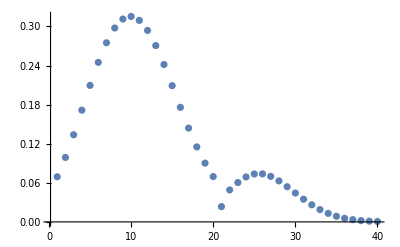

```mathematica
{DNmh,DNmhi}=matSqrts[DNorm,thresholdD];

{e0,v0}=Sort[Transpose[Eigensystem[tst=Transpose[DNmhi].DHam.DNmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&][[1]];
Print["B(D) = ",e0];
Print["Dim_full^deuteron = ",Dimensions[DNorm][[1]],"=^!",DBasisDim,"   ;     Dim_(non - singular)^deuteron = ",Dimensions[v0][[1]]]
fullv0=Normalize[Transpose[DNmh].v0];
ListPlot[Re[fullv0],PlotRange->Full]
```

#### Read LHS ⟨ ϕ_lit^n|(Ĥ)_(V18+UIX)|ϕ_lit^m ⟩, m,n∈{1,N_LIT}

```mathematica
matnames=("./mat_"<>ToString[#]<>"^-")&/@Subscript[I, n];
LitNormHamMat=readREAL8list[#]&/@matnames;

LITbasisDim=IntegerPart[Sqrt[Length[#] 0.5]]&/@LitNormHamMat;
LitNorm=ArrayReshape[LitNormHamMat[[#]][[1;;LITbasisDim[[#]]^2]],{LITbasisDim[[#]],LITbasisDim[[#]]}]&/@Range[1,Length[Subscript[I, n]]];LitHam=ArrayReshape[LitNormHamMat[[#]][[LITbasisDim[[#]]^2+1;;]],{LITbasisDim[[#]],LITbasisDim[[#]]}]&/@Range[1,Length[Subscript[I, n]]];
Print["N_LIT = ",LITbasisDim];
```

N_LIT = {80,80,80}

min/max: {-8.62174×10^-16,23.0083}

(min/max) discarded elements: 45 {-8.62174×10^-16,3.44434×10^-9}

J=0:  E_0=0.00894636

min/max: {-4.93681×10^-16,23.0083}

(min/max) discarded elements: 45 {-4.93681×10^-16,3.44434×10^-9}

J=1:  E_0=0.00894641

min/max: {-4.93681×10^-16,23.0083}

(min/max) discarded elements: 45 {-4.93681×10^-16,3.44434×10^-9}

J=2:  E_0=0.00894609

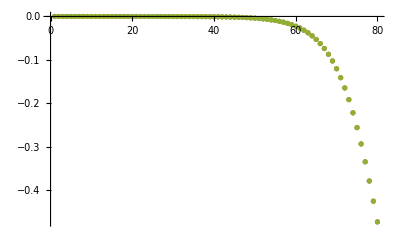

```mathematica
LitNmhis={};
fullv0l={};
Do[
{LitNmh,LitNmhi}=matSqrts[LitNorm[[nj]],thresholdLIT];
AppendTo[LitNmhis,{LitNmh,LitNmhi}];
{e0l,v0l}=Sort[Transpose[Eigensystem[tst=Transpose[LitNmhi].LitHam[[nj]].LitNmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&][[1]];
Print["J=",Subscript[I, n][[nj]],":  E_0=",e0l];
AppendTo[fullv0l,Normalize[Transpose[LitNmh].v0l]];
,{nj,Range[1,Length[Subscript[I, n]]]}
];

ListPlot[Re[fullv0l],PlotRange->Full]
```

#### Read RHS ⟨ ϕ_(lit+D3)^n|O_Lm_L|ϕ_(lit+D3)^m ⟩, n,m∈{1,N_LIT/n_k+N_D3}

the calculation is parallel in n_k parts

```mathematica
nk=Max[ToExpression[StringSplit[FileNames["*_S_*"],"_"][[All,1]]]];
ks=Range[0,nk];


CouplingBlockj={};
Do[
CouplingBlock={};
Do[
mM=Select[mLs,ClebschGordan[{multipolarity,#},{J0,mIn-#},{Subscript[I, n][[nj]],mIn}]≠0&];

CouplingBlocks={};
Do[
files="./"<>ToString[#]<>"_S_"<>ToString[Subscript[I, n][[nj]]]<>"_"<>ToString[mIn]<>"_"<>ToString[mL]<>".lit"&/@ks;
(*Print[files];*)
inhomos=readREAL8list[#]&/@files;
(*Print[inhomos];*)
CouplingMatrices=ArrayReshape[#,{Sqrt[Length[#]],Sqrt[Length[#]]}]&/@inhomos;
CouplingBloxx=#[[DBasisDim+1;;,;;DBasisDim]]&/@CouplingMatrices;
dims=Dimensions[#]&/@CouplingBloxx;
coupl=ClebschGordan[{multipolarity,mL},{J0,mIn-mL},{Subscript[I, n][[nj]],mIn}];
(*Print["Cell["⟨",ExpressionUUID->"bd464d2a-9896-4818-8e95-3a80604609bf"]",multipolarity,mL,J0,mIn-mL,"Cell["|",ExpressionUUID->"13991f8f-67e9-4a1b-a6b3-73645d6cc25a"]",Subscript[I, n][[nj]],mIn,"Cell["⟩",ExpressionUUID->"3c0ea77d-f898-4660-95b6-be7dddb2412d"] =  ",coupl];*)
(*Print[ArrayReshape[CouplingBloxx,{Total[dims[[All,1]]],DBasisDim}]//MatrixForm];*)
AppendTo[CouplingBlocks,coupl ArrayReshape[CouplingBloxx,{Total[dims[[All,1]]],DBasisDim}]];
,{mL,mM}
]

AppendTo[CouplingBlock,{mIn,Total[CouplingBlocks]}];
(*Print["m_I_n=",mIn,"  : ",Total[CouplingBlocks]//MatrixForm];*)
,{mIn,mIns[[nj]]}]

AppendTo[CouplingBlockj,CouplingBlock];
,{nj,Range[1,Length[Subscript[I, n]]]}]

Print["Dim(⟨ψ|ο̂|deuteron⟩) = ",Dimensions[CouplingBlockj[[#]][[1]][[2]]&/@Range[1,Length[Subscript[I, n]]]]];
Print["Dim(⟨ψ|Ĥ|ψ⟩) = ",Dimensions[LitHam]];
Print["Dim(⟨ψ|OverHat[1]|ψ⟩) = ",Dimensions[LitNorm]];
```

Dim(⟨ψ|ο̂|deuteron⟩) = {3,80,40}

Dim(⟨ψ|Ĥ|ψ⟩) = {3,80,80}

Dim(⟨ψ|OverHat[1]|ψ⟩) = {3,80,80}

#### “algebraic” LIT (norm zero-mode removal)

L_ν'L'νL^(I_f I_i;I_n)(k,k;σ)=(-)^(I_n-I_i+L-L'+ν')ρ(I_n,σ)∑_M_n ⟨ψ_(I_f I_i M_n)^ν'L'(k,σ)|ψ_(I_f I_i M_n)^νL(k,σ)⟩

```mathematica
(*SetSharedVariable[testcompo,testfu]*)
σI=4.0;
σRmin=-10.;σRmax=100.;σRstep=1;
σRs=Range[σRmin,σRmax,σRstep];
testfu=0;
```

```mathematica
Clear[normreg];
normreg[threshold_,noMa_]:=Block[
{es=Eigensystem[noMa],μ,transf},
{μ,transf}=Transpose[Select[Transpose[es],#[[1]]>threshold&]];
(Transpose[transf].DiagonalMatrix[μ^(-1/2)])];

Clear[decompose];
decompose[thresholdD_,thresholdLIT_,DNorm_,DHam_,LITNorm_,LITHam_,LITYD_]:= Block[{OμRHS,λsD,trfD,OμLHS,λsLit,trfLit,inhomo,egs,evgs},
OμRHS=normreg[thresholdD,DNorm];
{λsD,trfD}=Eigensystem[(Transpose[OμRHS].DHam).OμRHS];
egs=Min[λsD];
evgs=Flatten[trfD[[TakeSmallest[λsD->"Index",1]]]];

OμLHS=normreg[thresholdLIT,LITNorm];
{λsLit,trfLit}=Eigensystem[(Transpose[OμLHS].LITHam).OμLHS];

Print["E_0( th=",N[thresholdD]," ) = ",egs,"    dim(D,LIT) = ",Dimensions[λsD],Dimensions[λsLit]];

inhomo=(Transpose[OμLHS].(LITYD.OμRHS)).evgs;
{λsLit,(trfLit.inhomo)^2,egs}
];
Clear[litcomp];
litcomp[thresholdD_,thresholdLIT_,DNorm_,DHam_,LITNorm_,LITHam_,LITYD_]:=Block[{λscf=decompose[thresholdD,thresholdLIT,DNorm,DHam,LITNorm,LITHam,LITYD]},
egrnd=λscf[[3]];
tmpp=Transpose[λscf[[;;2]]];
Plus@@((#[[2]]/((#[[1]]-egrnd-σRe)^2+σI^2))&/@tmpp)];
```

```mathematica
Clear[LIT,LITs,testfu];

minth=thresholdLIT;maxth=.02 thresholdLIT;nth=1;
If[nth==1,thresholdrng={thresholdLIT},thresholdrng=Range[minth,maxth,(maxth-minth)/nth]];

LITsj={};

Do[
testfu={};
Print["I_n=",Subscript[I, n][[nj]]];
Do[

tmp=CouplingBlockj[[nj]][[mm]][[2]];

AppendTo[testfu,(-1)^(Subscript[I, n][[nj]]-J0+mm) Evaluate[litcomp[#,#,DNorm,DHam,LitNorm[[nj]],LitHam[[nj]],tmp]&/@thresholdrng]];

,{mm,Length[mIns[[nj]]]}
];

AppendTo[LITsj,Total[testfu]/.σRe->σRs];
,{nj,Range[1,Length[Subscript[I, n]]]}
]

thrlegend=("λ_𝟙="<>ToString[#,TraditionalForm]&/@thresholdrng);
pltlabs="I_n="<>ToString[#]&/@Subscript[I, n]

plote=ListPlot[Flatten[(Transpose[{σRs,#}]&/@LITsj[[#]])&/@Range[1,Length[Subscript[I, n]]],1],
PlotLabel->Style["σ_I = "<>ToString[σI]<>"    ; J_lit = "<>ToString[Subscript[I, n]],18,Red],
AxesLabel->{Style["σ_R [MeV]",Gray,18],Style["LIT [MeV^-4]",Red,18]},
PlotLegends->Placed[thrlegend,Above],
LabelStyle->12,ImageSize->ImgSize,PlotRange->Full,PlotLabels->pltlabs,
Mesh->5,MeshFunctions->{#2&,#2&,#2&},PlotMarkers->{Automatic,Scaled[0.01 #]}&/@Range[1,nth],
Joined->True];
Export["plot.pdf",plote,"PDF","AllowRasterization"->False]
```

I_n=0

E_0( th=5.40269×10^-9 ) = -2.22233    dim(D,LIT) = {40}{35}

I_n=1

E_0( th=5.40269×10^-9 ) = -2.22233    dim(D,LIT) = {40}{35}

E_0( th=5.40269×10^-9 ) = -2.22233    dim(D,LIT) = {40}{35}

E_0( th=5.40269×10^-9 ) = -2.22233    dim(D,LIT) = {40}{35}

I_n=2

E_0( th=5.40269×10^-9 ) = -2.22233    dim(D,LIT) = {40}{35}

E_0( th=5.40269×10^-9 ) = -2.22233    dim(D,LIT) = {40}{35}

E_0( th=5.40269×10^-9 ) = -2.22233    dim(D,LIT) = {40}{35}

«2 more identical outputs»

{I_n=0,I_n=1,I_n=2}

plot.pdf

E_0( th=5.40269×10^-9 ) = -2.22233    dim(D,LIT) = {40}{35}

E_0( th=5.40269×10^-9 ) = -2.22233    dim(D,LIT) = {40}{35}

E_0( th=5.40269×10^-9 ) = -2.22233    dim(D,LIT) = {40}{35}

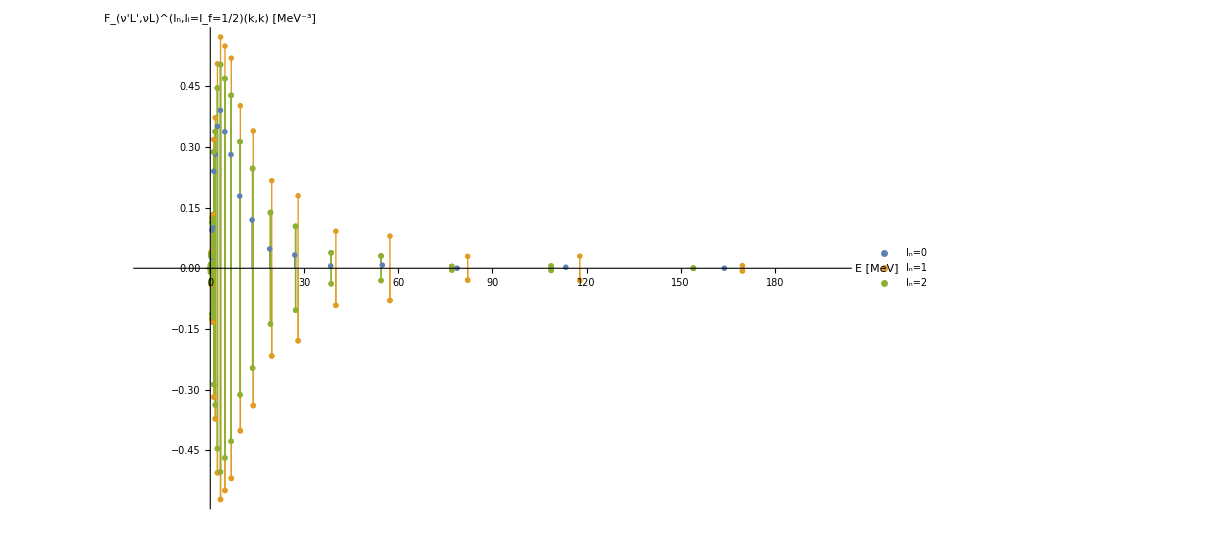
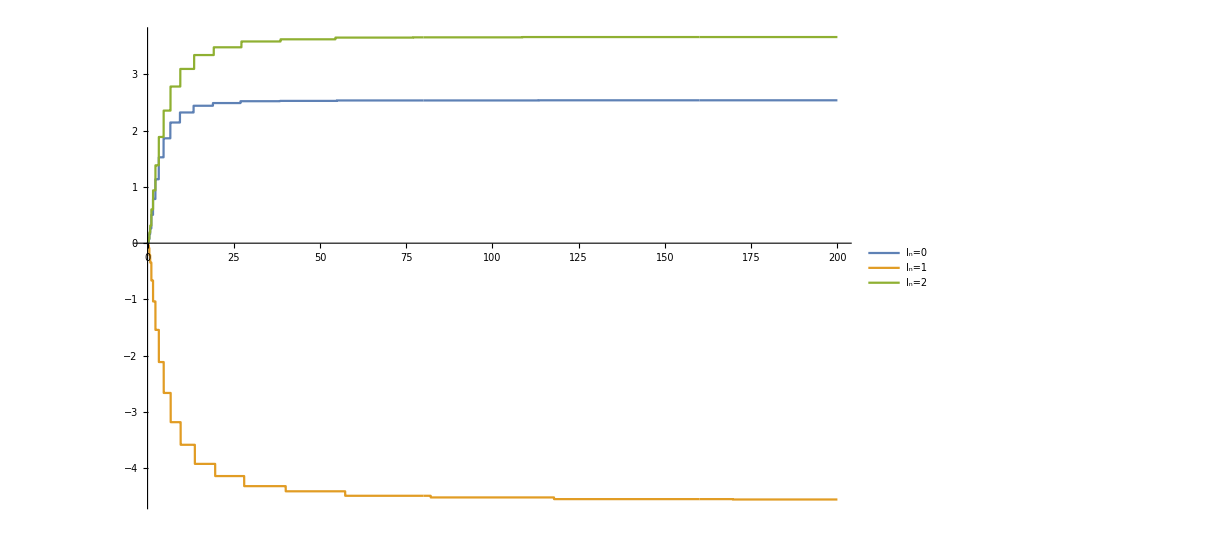

delta_strength_function_deuteron.pdf

```mathematica
Clear[thresh,es,μ,transf];
lpsis={};CumStrengths={};

es=Eigensystem[DNorm];
{μ,transf}=Transpose[Select[Transpose[es],Re[#[[1]]]>thresholdD&]];
OμRHS=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);

{λsD,trfD}=Eigensystem[(Transpose[OμRHS].DHam).OμRHS];
evgs=Flatten[trfD[[TakeSmallest[λsD->"Index",1]]]];
egs=Min[λsD];
leg={};
Do[
lpsi={};
esl=Eigensystem[LitNorm[[nj]]];
{μl,transfl}=Transpose[Select[Transpose[esl],Re[#[[1]]]>thresholdLIT&]];
OμLHS=(Transpose[transfl].DiagonalMatrix[μl^(-1/2)]);
{λsLit,trfLit}=Eigensystem[(Transpose[OμLHS].LitHam[[nj]]).OμLHS];

Print["E_0( th=",N[thresholdD]," ) = ",egs,"    dim(D,LIT) = ",Dimensions[λsD],Dimensions[λsLit]];

Do[
inhomo=(Transpose[OμLHS].(CouplingBlockj[[nj]][[mm]][[2]].OμRHS)).(evgs);
AppendTo[lpsi,Transpose[{λsLit,(-1)^(Subscript[I, n][[nj]]-J0+mm) (trfLit.inhomo)^2}]];

,{mm,Length[mIns[[nj]]]}
];

AppendTo[lpsis,Flatten[lpsi,1]];
AppendTo[leg,"I_n="<>ToString[Subscript[I, n][[nj]]]];

Egrid=Range[1.001 Min[Re[lpsis[[1]][[All,1]]]],200,0.01];

AppendTo[CumStrengths,Transpose[{Egrid,Table[Total[Select[Re[lpsis[[-1]]],#[[1]]<Egrid[[ee]]&]][[2]],{ee,1,Length[Egrid]}]}]];

,{nj,Range[1,Length[Subscript[I, n]]]}
]


plote3=Grid[{{
ListPlot[lpsis,Joined->False,PlotMarkers->{{♪,12},{♔,12},{♗,12}},Filling->Axis,FillingStyle->{{Blue},{Green},{Red}},PlotRange->{{-20,200},Full},AxesLabel->{Style["E [MeV]",18],Style["F_(ν'L',νL)^(I_n,I_i=I_f=1/2)(k,k) [MeV^-3]",18]},PlotStyle->{},PlotLegends->leg,ImageSize->ImgSize]
},{
ListPlot[CumStrengths,Joined->True,ImageSize->ImgSize,PlotRange->{Automatic,Automatic},PlotLegends->leg]
}}]
Save[tmpDir<>"/lpsis.plot_"<>ToString[IntegerPart[AbsoluteTime[Now]-AbsoluteTime[Today]]],lpsis]
Save[tmpDir<>"/CumStrength.plot_"<>ToString[IntegerPart[AbsoluteTime[Now]-AbsoluteTime[Today]]],CumStrengths]
Export["delta_strength_function_deuteron.pdf",plote3,"PDF","AllowRasterization"->False]
```

#### S(E)=∑_m Ψ_m^2·δ(E-λ_m) → S_benign(E)

C(E):=∫E/0 dΔ S(Δ)=∑_(N_(n,d)) Poly[E,N_numerator]/Poly[E,N_denominator-1]
s.t. C(0)=0
F(E)=(∂C)/(∂E)

{{cnum[1]→11.2126,cnum[2]→11.6664,cnum[3]→-0.00179821,cnum[4]→6.07084×10^-6,cdenom[1]→56.4142,cdenom[2]→5.08888,cdenom[3]→4.53866},{cnum[1]→-0.762821,cnum[2]→-13.0107,cnum[3]→0.00383537,cnum[4]→-9.51807×10^-6,cdenom[1]→20.6781,cdenom[2]→8.5857,cdenom[3]→2.72563},{cnum[1]→35.5693,cnum[2]→76.1461,cnum[3]→-0.0372835,cnum[4]→0.000105812,cdenom[1]→207.873,cdenom[2]→46.7142,cdenom[3]→19.6772}}

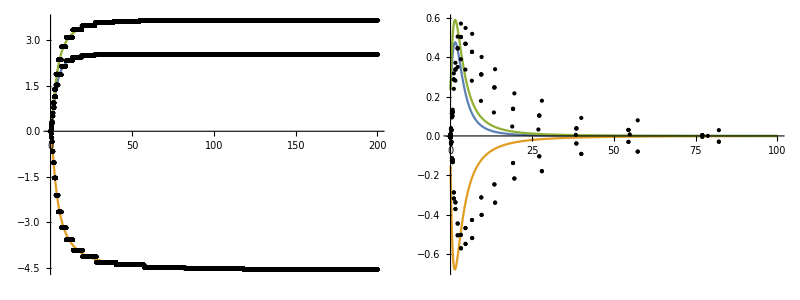

```mathematica
data=CumStrengths;
ordnum=4;orddenom=3;
coffs={Array[cnum,ordnum],Array[cdenom,orddenom]};
inicoffs=Transpose[{Flatten[coffs],RandomReal[{0.01,1.2},Length[Flatten[coffs]]]}];
num=Sum[coffs[[1]][[n]] t^n,{n,ordnum}];
denom=Sum[coffs[[2]][[n+1]] t^n,{n,0,orddenom-1}];
model=num/denom;

optPOSsol=
FindFit[#,{model,coffs[[2]][[1]]>0},inicoffs,t,MaxIterations->1500(*,PrecisionGoal->10,AccuracyGoal->10*),Method->Automatic]&/@data
(*CumStr[e_]:=model/.optPOSsol/.t->x
StrC[e_]:=D[model/.optPOSsol,t]/.t->e*)
Cums=model/.#/.t->tt&/@optPOSsol;
StrC=(D[model/.#,t]/.t->e2)&/@optPOSsol;
Grid[{{Plot[Cums,{tt,0,CumStrengths[[1]][[All,1]][[-1]]},Epilog->{PointSize[Small],Point[#]&/@CumStrengths},PlotRange->Full,ImageSize->ImgSize],Plot[StrC,{e2,0.1,100},Epilog->Map[Point,lpsis],PlotRange->Full,ImageSize->ImgSize]}}]
```

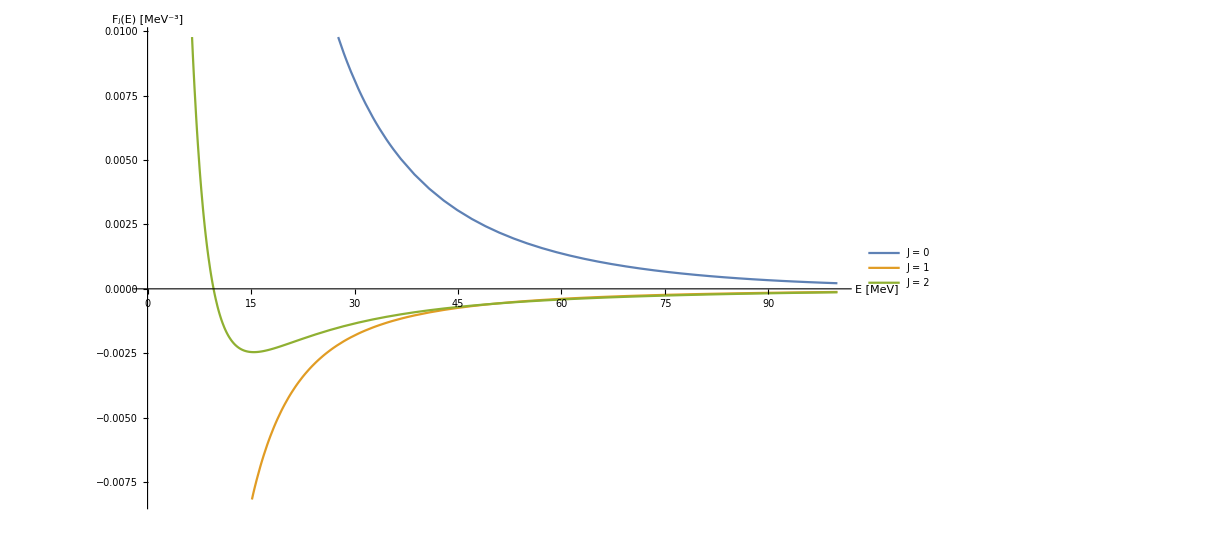

```mathematica
responseListJ={};

jJtot={0,1,2};
Do[
responseListI={};
Do[
SixJ=SixJSymbol[{1,1,jJtot[[nj]]},{1,1,Subscript[I, n][[nIn]]}];
response=SixJ StrC[[nIn]];
AppendTo[responseListI,response];
,{nIn,Range[1,Length[Subscript[I, n]]]}
];
AppendTo[responseListJ,Total[responseListI]];
,{nj,Range[Length[jJtot]]}
];

labeljlit=("J = "<>ToString[#])&/@jJtot;

Plot[responseListJ,{e2,0,100},PlotRange->{{0,100},Automatic},PlotLegends->Placed[labeljlit,Bottom],AxesLabel->{"E [MeV]","F_j(E) [MeV^-3]"},LabelStyle->Directive[Larger],ImageSize->ImgSize]
```

#### real and imaginary parts of the (generalized) polarizabilities from strength functions

{P_(if,J)^res(M^ν' L',M^ν L,k',k)}_imag=2 π^2 (-)^(L+I_f+I_i)L̂ L̂' [F_((ν'L'νL)J)^(I_f I_i)(k,k;E_i+k)+(-)^(L+L'+J)F_((ν'L'νL)J)^(I_f I_i)(k,k;E_i-k')]
The second term does not contribute because the initial state is the ground- and not an excited state!

ECCE: the L̂’s come from the multipole expansion of the plane wave as do the 2π’s
ImPList [I_(n=1),I_(n=2),...] [fit_1,fit_2,...] [k_0... k_max]

#### imaginary part of the amplitude and total photodisintegration cross-section

{T_(L_f λ_f;L_i λ_i)^(I_f M_f;I_i M_i)(k⃗',k⃗)}_imag=(-)^(1+λ_f+I_f-M_i) ∑_(M_L_f M_L_i J) (-)^(L_i+L_f) (L̂)^2(I_f | J | I_i
-M_f | m | M_i) (L_i | L_f | J
M_i | M_f | -m) {P_(if,J)^(L_f λ_f,L_i λ_i)(k',k)}_imag D_(M_f,-λ_f)^L_f(0,θ,0) 

ECCE: 
i)   the polarization λ affects magnetic multipole ME’s, only (see eqs. (27,29,41) )
ii)  k⃗||(e⃗)_z ⇒ D_(M,λ)^L(R)=1
iii) fm^2=10^-2 b=10mb
iv) σ(M^ν L)=(-)^(L+1)(4π)/(√(2 J_i+1)·√(2 L+1)k) ImP_0 
      from eq.(4.38) “H. Arenhoevel -- SUBNUCLEAR DEGREES OF FREEDOM IN PHOTOABSORPTION AND SCATTERING in new vistas...

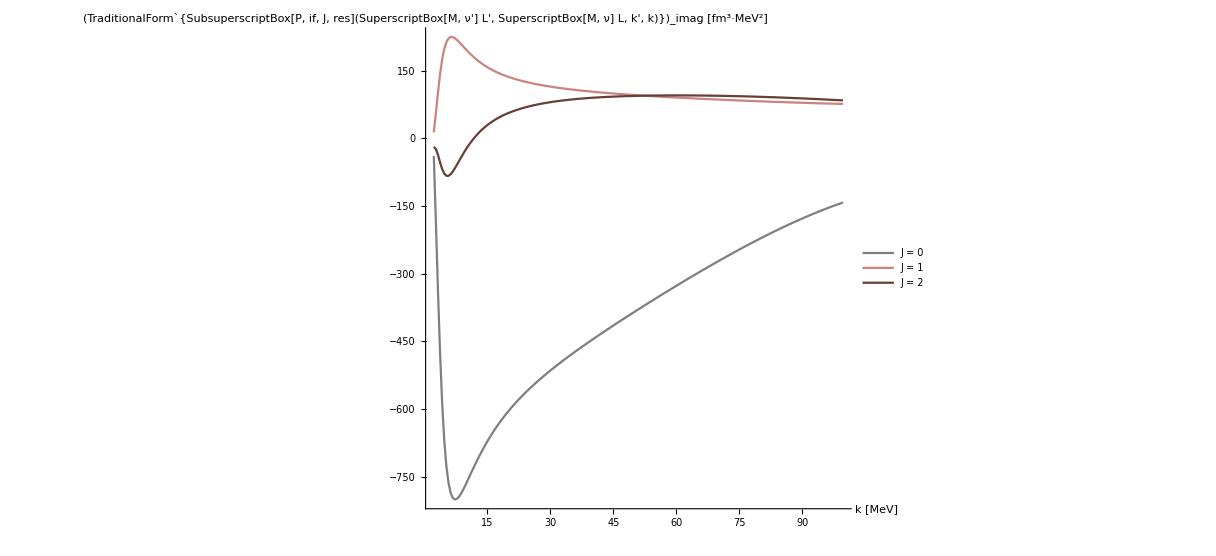

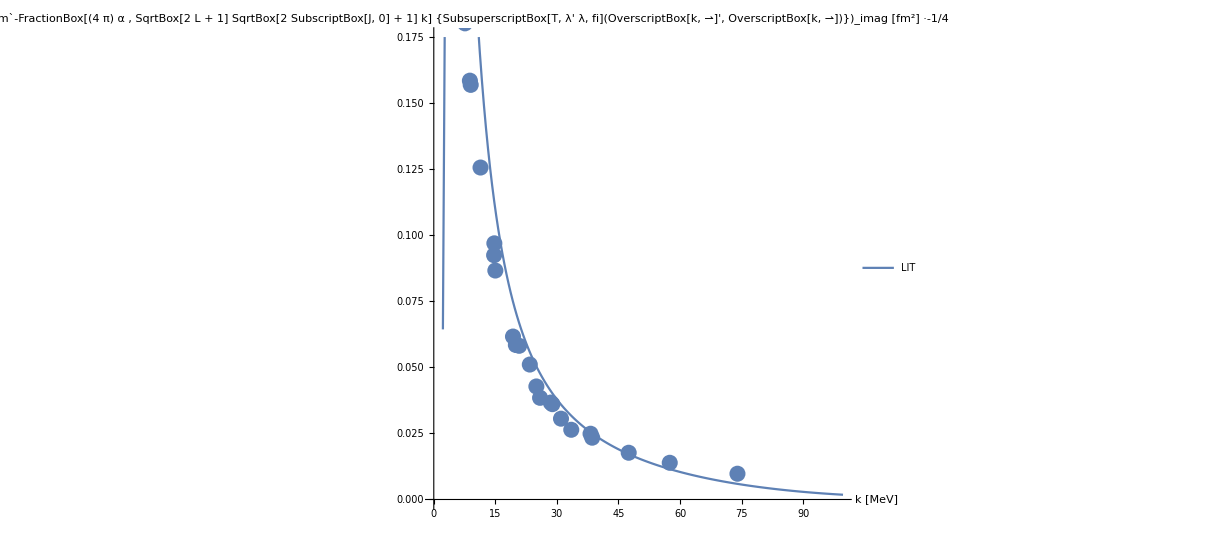

```mathematica
Clear[ee,e2];
k0=0.001;k1=100;dK=0.5;
kσ=Range[Abs[e0],k1,dK];
Ji=Jf=J0;Mi=Ji;Mf=Mi;
Jj=jJtot;
labelj=("J = "<>ToString[#])&/@Jj;
strengthfunctionList=Table[Table[((ee-e0)^2 responseListJ[[nJ]]/.e2->ee)/.ee->(e0+kmag),{kmag,kσ}],{nJ,Range[1,Length[jJtot]]}];

ImPList=2 Pi^2 (-1)^(multipolarity+Jf+Ji) hat[multipolarity] hat[multipolarity] strengthfunctionList;
z=List[];

For[nJ=1,nJ≤Length[Jj],nJ++,(
atmp=ListLinePlot[ImPList[[nJ,All]],PlotRange->Full,LabelStyle->Directive[Larger],AxesLabel->{"k [MeV]","(TraditionalForm`{SubsuperscriptBox[P, if, J, res](SuperscriptBox[M, ν'] L', SuperscriptBox[M, ν] L, k', k)})_imag [fm^3·MeV^2]"},ImageSize->ImgSize,Joined->True,DataRange->{Min[kσ],Max[kσ]},PlotStyle->{ColorData[7,"ColorList"][[nJ]]},PlotLegends->{labelj[[nJ]]}];
AppendTo[z,atmp];
)];
Show[z,PlotRange->All]

ImT[Mf_,Mi_,λf_,θ_]:=
Module[{compo},
ampli=0;
For[nJ=1,nJ≤Length[Jj],nJ++,(
compo=hat[Jj[[nJ]]]^2 ImPList[[nJ,All]];
For[Mm=-multipolarity,Mm≤multipolarity,Mm++,(
For[Mmp=-multipolarity,Mmp≤multipolarity,Mmp++,
(
ampli+=ThreeJSymbol[{Jf,-Mf},{Jj[[nJ]],Mf-Mi},{Ji,Mi}] ThreeJSymbol[{multipolarity,Mm},{multipolarity,Mmp},{Jj[[nJ]],-Mm-Mmp}] WignerD[{multipolarity,Mmp,-λf},0,θ,0] compo;
)];)];)];
Return[(-1)^(1+λf+Jf-Mi)*ampli]
]
fudgi=-1/4;
kinfac=(-1)^(multipolarity+1)(fudgi 4 Pi)/(√(2 J0+1) √(2 multipolarity+1) kσ 137);

DissCross[Mf_,Mi_,λf_,θ_,kinfac_]:=kinfac ImT[Mf,Mi,λf,θ];
lf=1;
Show[ListPlot[Re[DissCross[Jf,Ji,lf,0,kinfac]],PlotRange->Automatic,LabelStyle->Directive[Larger],AxesLabel->{"k [MeV]","(TraditionalForm`-FractionBox[(4  π) α , SqrtBox[2  L + 1] SqrtBox[2 SubscriptBox[J, 0] + 1] k] {SubsuperscriptBox[T, λ' λ, fi](OverscriptBox[k, ⇀]', OverscriptBox[k, ⇀])})_imag [fm^2] ·"<>ToString[Style[fudgi,Red],TraditionalForm]}(*,Filling->cycl*),ImageSize->ImgSize,Joined->{True,False},DataRange->{Min[kσ],Max[kσ]},PlotLegends->{"LIT","σ_tot data"}],
ListPlot[DeutDataFm2]]
```